```mathematica
vgg16Net=NetModel["VGG-16 Trained on ImageNet Competition Data","UninitializedEvaluationNet"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net2=NetReplacePart[NetTake[vgg16Net,{"conv1_1","pool5"}],"Input"->NetEncoder[{"Image",100}]]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net2,"b1"->BatchNormalizationLayer[],"conv1_2"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b2"->BatchNormalizationLayer[],"conv2_1"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b3"->BatchNormalizationLayer[],"conv2_2"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b4"->BatchNormalizationLayer[],"conv3_1"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b5"->BatchNormalizationLayer[],"conv3_2"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b6"->BatchNormalizationLayer[],"conv3_3"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b7"->BatchNormalizationLayer[],"conv4_1"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b8"->BatchNormalizationLayer[],"conv4_2"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b9"->BatchNormalizationLayer[],"conv4_3"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b10"->BatchNormalizationLayer[],"conv5_1"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b11"->BatchNormalizationLayer[],"conv5_2"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b12"->BatchNormalizationLayer[],"conv5_3"]
```

```mathematica
NetChain[<>]
```

```mathematica
vgg16Net4=NetChain[{vgg16Net3,LinearLayer[1]}]
```

```mathematica
NetChain[<>]
```

```mathematica
dataDirectory="C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2\\";
```

```mathematica
ids=Map[FileBaseName,Map[FileNameTake,FileNames[___~~".mx",dataDirectory]]];
```

```mathematica
Export["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx",ids]
```

C:\Users\rbc15\Desktop\Mathematica\MLNamesData2.mx

```mathematica
Length[ids]
Length[mxs]
```

164913

164913

```mathematica
ids=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx"]
```

{00002bf3-e652-4937-b5b7-da80bc8794e6,00009198-253e-4028-a689-6a64578d99ea,0000aaf4-d0a7-42b6-9220-2a138237794b,164908,fffe7f0d-a317-453d-a358-c8f0384e441a,fffeda98-7be8-4da1-90af-4ccf9bb957e9}
 |  |  |  |

```mathematica
mxs=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2.mx"]
```

<|00002bf3-e652-4937-b5b7-da80bc8794e6→{35500,37500,6500,1000,28500,26500,50000,22500,39500,24000},164911,fffeda98-7be8-4da1-90af-4ccf9bb957e9→{9500,26500,3000,39500,2500,31000}|>
 |  |  |  |

```mathematica
mxs=AssociationMap[Import[FileNameJoin[{dataDirectory,StringJoin[#,".mx"]}]]&,ids];
```

```mathematica
Export["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2.mx",mxs]
```

C:\Users\rbc15\Desktop\Mathematica\MLData2.mx

```mathematica
data=Flatten[Map[{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]->{Max[mxs[[Key[#]]]]}}&,ids]];
```

```mathematica
{training,testing}=TakeDrop[RandomSample[data],161000];
```

```mathematica
sample=RandomSample[testing,10]
```

{File[C:\Users\rbc15\Desktop\Mathematica\MLData2\a2c26ebd-69c4-4efa-8775-8b06b4a73a5a.jpg]→{40500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\710f93f2-3f6d-4bc9-8bd8-d0a367cada92.jpg]→{49500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\baee5664-7fa1-4f06-a360-dd440ac9e172.jpg]→{46500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\0583dff6-5f61-442a-90a8-6aae958e83bc.jpg]→{44500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\a27f9d5c-3447-4416-9ed6-97d776392ba2.jpg]→{48500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\30944587-142e-4fde-b9cc-54c7beee9f51.jpg]→{50000},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\395e44d2-865a-452e-9a5a-3889593f3e1f.jpg]→{48500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\5457a1a0-f521-4757-8109-dfdf1d340c08.jpg]→{40500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\e3262a9a-0d8a-4686-b478-73252e9eb837.jpg]→{50000},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\d6e07f6d-b17a-4779-a149-5600bcf7d303.jpg]→{49000}}

```mathematica
vgg16NetTrained=NetTrain[vgg16Net4,training,ValidationSet->testing,TargetDevice->"GPU",BatchSize->32]
```

NetChain[<>]

```mathematica
Export["MaxLength2.wlnet",vgg16NetTrained]
```

MaxLength2.wlnet

```mathematica
vgg16NetTrained=Import["MaxLength2.wlnet"]
```

NetChain[<>]

```mathematica
vgg16NetTrained[sample[[All,1]]]
sample[[All,2]]
Map[Import,sample[[All,1]]]
```

{{48550.8},{41537.5},{40172.7},{34302.2},{43740.1},{48262.8},{45129.9},{19226.5},{48621.3},{49782.4}}

{{47500},{41000},{40000},{34000},{43500},{48500},{45000},{19000},{48000},{50000}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
class[list_,nbins_]:=Map[Floor[(#/Max[list])*nbins]&,list]
```

```mathematica
listData=Flatten[Map[{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]->class[mxs[[Key[#]]],20]}&,ids]];
```

```mathematica
{traininglist,testinglist}=TakeDrop[RandomSample[listData],161000];
```

```mathematica
loss=CTCLossLayer[]
```

CTCLossLayer[<>]

```mathematica
classes=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
decoder=NetDecoder[{"CTCBeamSearch",classes}]
```

NetDecoder[<>]

```mathematica
convUnit[c_]:=NetChain[{ConvolutionLayer[c,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2]}]
```

```mathematica
ocrNet=NetChain[{convUnit[50],convUnit[50],convUnit[50],convUnit[50],convUnit[10],TransposeLayer[1<->3],FlattenLayer[-1],GatedRecurrentLayer[50],GatedRecurrentLayer[50],NetMapOperator[LinearLayer[Length[classes]+1]],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",100,"Grayscale"}],"Output"->decoder]
```

NetChain[<>]

```mathematica
ocrNetTrained=NetTrain[ocrNet,traininglist,ValidationSet->testinglist,LossFunction->loss,BatchSize->32,TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
Export["RelativeHeight2.wlnet",ocrNetTrained]
```

RelativeHeight2.wlnet

```mathematica
ocrNet1=Import["RelativeHeight.wlnet"]
```

NetChain[<>]

```mathematica
samplelist=RandomSample[testinglist,10];
```

```mathematica
predictions=ocrNetTrained[samplelist[[All,1]]];
```

```mathematica
solutions=samplelist[[All,2]];
```

```mathematica
inputs=Map[Import,samplelist[[All,1]]];
```

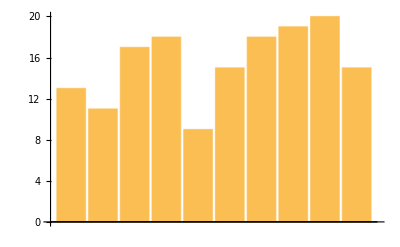
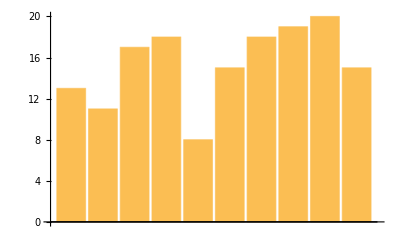
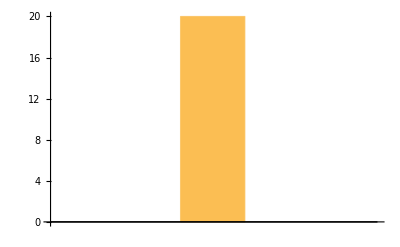
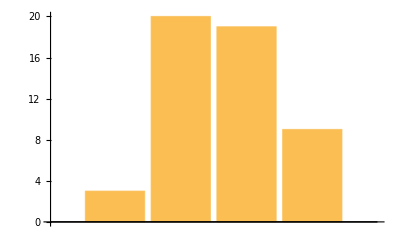
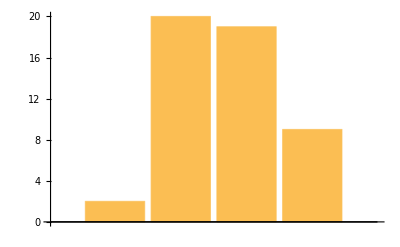
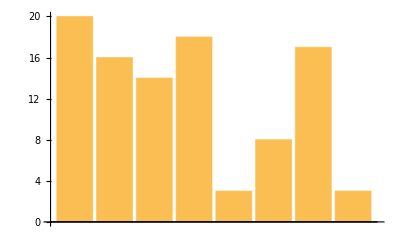
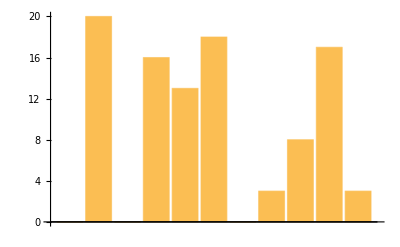
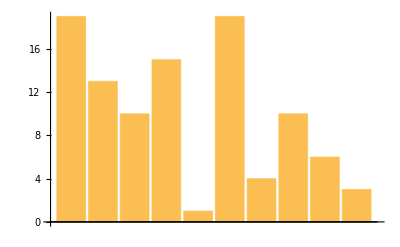
Input | Output | expected Output
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[Map[{Show[Import[#[[1]]],ImageSize->200],BarChart[ocrNetTrained[#[[1]]]],BarChart[#[[2]]]}&,samplelist],
{"Input", "Output", "expected Output"}],Frame->All]
```

variable length images

```mathematica
ocrNetTrained[-Graphics-,{"TopDecodings",5}]
```

{{4,18,20,16},{4,19,20,16},{4,18,20},{3,18,20,16},{4,20,16}}

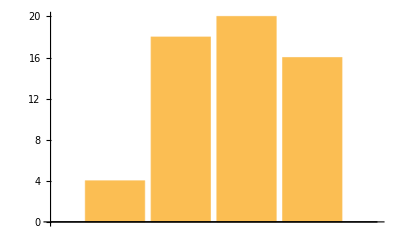
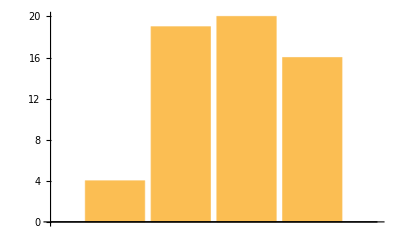
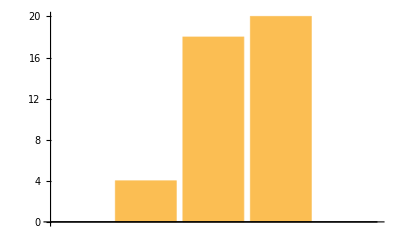
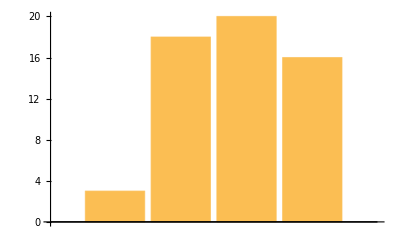
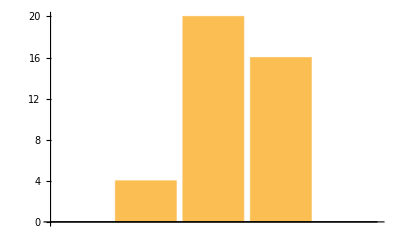

```mathematica
Map[BarChart[#]&,%]
```

## Combining the networks

```mathematica
readGraph[graph_]:=Flatten[Map[#*(vgg16NetTrained[graph]/20)&,ocrNetTrained[graph]]]
SetAttributes[readGraph,Listable]
```

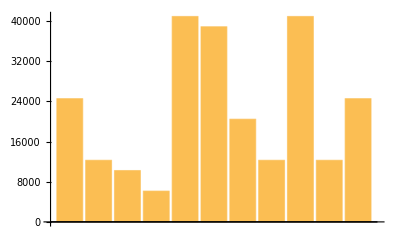
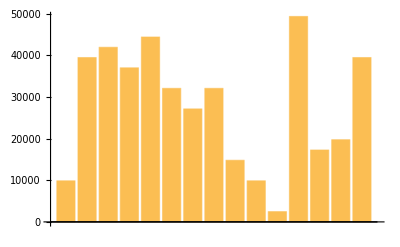
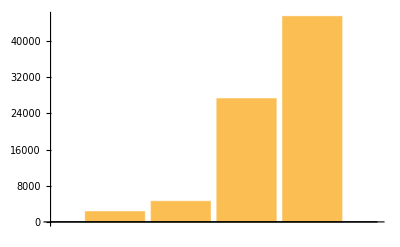
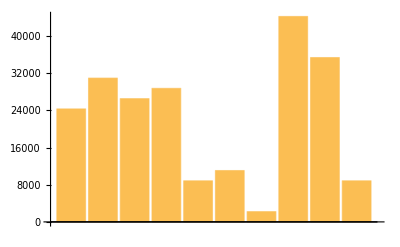
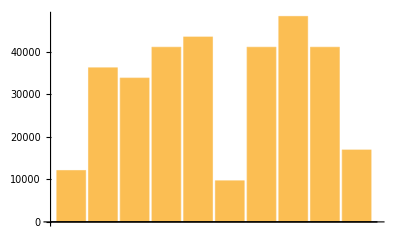
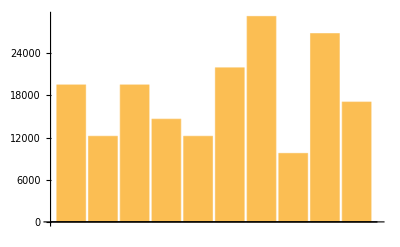
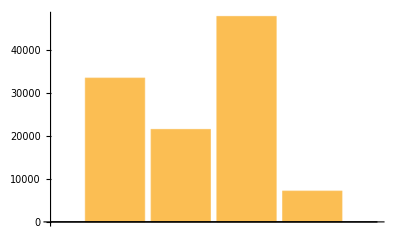
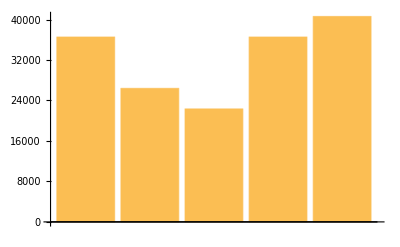
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[{Import[#],BarChart[readGraph[#]]}&,sample[[All,1]]]
```

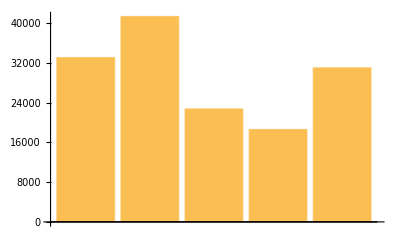
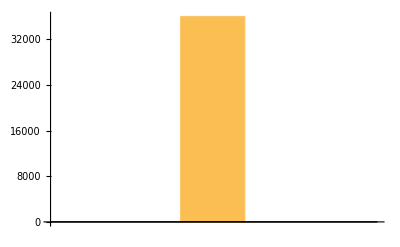
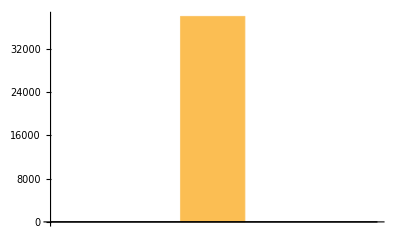
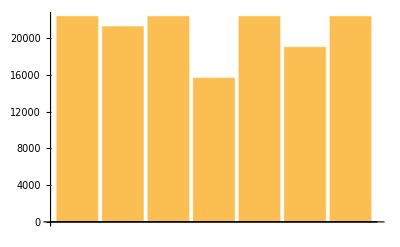
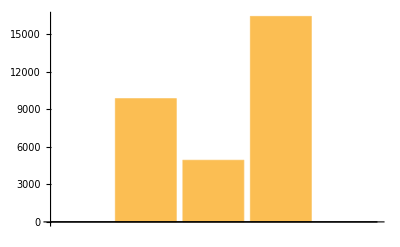
Chart | Interpretation
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Prepend[Map[{Show[#,ImageSize->200],BarChart[readGraph[#]]}&,],{"Chart","Interpretation"}],Frame->All]
```